## Tissue-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51h (15 June 2017)) loaded Sun 18 Jun 2017 09:44:42
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

There are 8 cells in the tissue.

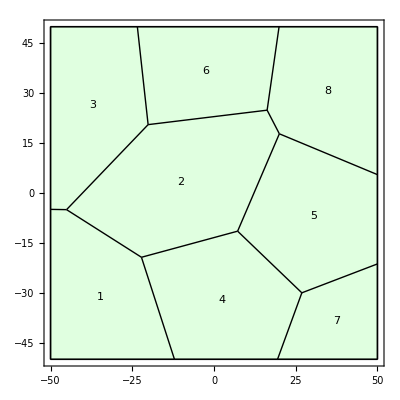

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Print["There are ", NTissueCells[q], " cells in the tissue."];  
ShowTissue[q, "CellNumbers"-> True, Frame-> True]
```

```mathematica
q
```

Tissue[{{-45.0975,-5.0017},{-22.19,-19.3181},{-20.1512,20.5505},{7.22701,-11.4733},{16.2501,24.895},{19.9897,17.7943},{26.8659,-30.0045},{50,-50},{50,50},{-50,50},{-50,-50},{50.,-21.3129},{50.,5.51685},{19.9059,50.},{-23.4467,50.},{-50.,-4.92181},{-12.0901,-50.},{19.4283,-50.}},{{1,2},{1,3},{1,16},{2,4},{2,17},{3,5},{3,15},{4,6},{4,7},{5,6},{5,14},{6,13},{7,12},{7,18},{8,12},{8,18},{9,13},{9,14},{10,15},{10,16},{11,16},{11,17},{12,13},{14,15},{17,18}},{{22,5,1,3,21},{2,1,4,8,10,6},{20,3,2,7,19},{25,14,9,4,5},{23,12,8,9,13},{24,7,6,11},{13,14,16,15},{18,11,10,12,17}}]